<<"MultivariateStatistics`";<<"Statistics`NormalDistribution`";

```mathematica
Hyperlink["Source. Please the bottom of the site!","http://www.bioinf.ucd.ie/people/ian/"]
```

```mathematica
Hyperlink["Source. Please the bottom of the site!","http://www.bioinf.ucd.ie/people/ian/Alon.txt"]
```

```mathematica
yk=Import["http://www.bioinf.ucd.ie/people/ian/Alon.txt","table"];
yk//Dimensions
```

{2001}

```mathematica
yk=Import["https://github.com/n-yougo/dataset/raw/master/Alon.txt","table"];
yk//Dimensions
```

{2001}

```mathematica
T1=Drop[Transpose[Drop[yk,1]],1]/10;
```

```mathematica
v2={2,4,6,8,10,12,14,16,18,20,22,24,39,42,43,48,50,51,54,55,60,62};
```

```mathematica
v1={1,3,5,7,9,11,13,15,17,19,21,23,25,26,27,28,29,30,31,32,33,34,35,36,37,38,40,41,44,45,46,47,49,52,53,56,57,58,59,61};
```

```mathematica
V[1]=Table[Part[T1,Part[v1,i]],{i,1,40}];
```

```mathematica
V[2]=Table[Part[T1,Part[v2,i]],{i,1,22}];
```

```mathematica
m[1]=Length[V[1]];m[2]=Length[V[2]];
```

```mathematica
Del=Norm[Mean[V[1]]-Mean[V[2]]]^2-Total[Variance[V[1]]]/m[1]-Total[Variance[V[2]]]/m[2];
```

```mathematica
Sig1=Total[Variance[V[1]]];Sig2=Total[Variance[V[2]]];p=Length[Transpose[V[1]]];
```

```mathematica
Sig1/Del
```

3.98964

```mathematica
Sig2/Del
```

3.95918

```mathematica
γ[a_]:=(a^-1 Log[a])^(1/2)
```

```mathematica
Do[n[pi]=Length[V[pi]];
mean[pi]=Mean[V[pi]];Cov[pi]=Covariance[V[pi]];SD[pi]=(V[pi]-Table[mean[pi],n[pi]]).Transpose[V[pi]-Table[mean[pi],n[pi]]]/(n[pi]-1);
{val[pi],vec[pi]}=Eigensystem[SD[pi]];
(*Noise Reduction Methodology*)
Do[NRVal[pi,i]=val[pi][[i]]-(Tr[SD[pi]]-Sum[val[pi][[l]],{l,1,i}])/(n[pi]-1-i);
NRVec[pi,i]=((n[pi]-1)NRVal[pi,i])^(-1/2)Transpose[V[pi]-Table[mean[pi],n[pi]]].vec[pi][[i]]
,{i,1,n[pi]-2}];
(*Cross Data Methodology*)
n[pi,1]=Ceiling[n[pi]/2];n[pi,2]=n[pi]-n[pi,1];CrossData[pi,1]=Take[V[pi],n[pi,1]];CrossData[pi,2]=Take[V[pi],-n[pi,2]];
Do[CrossMean[pi,i]=Mean[CrossData[pi,i]],{i,1,2}];
SDCross[pi]=(CrossData[pi,1]-Table[CrossMean[pi,1],{n[pi,1]}]).Transpose[CrossData[pi,2]-Table[CrossMean[pi,2],{n[pi,2]}]]/((n[pi,1]-1)(n[pi,2]-1))^(1/2);
SDCross2[pi]=SDCross[pi].Transpose[SDCross[pi]];
{SDVal2[pi],SDVec[pi]}=Eigensystem[SDCross2[pi]];
SDVal[pi]=SDVal2[pi]//Sqrt;
Ψ[pi,1]=Tr[SDCross2[pi]];
Do[Ψ[pi,i]=Tr[SDCross2[pi]]-Sum[SDVal2[pi][[j]],{j,1,i-1}],{i,2,n[pi,2]}];
Do[ϵ[pi,i]=NRVal[pi,i]/Tr[Cov[pi]];η[pi,i]=(SDVal2[pi][[i]])/Ψ[pi,i];τ[pi,i]=(*1-(SDVal2[pi][[i]])/Ψ[pi,i]*)Ψ[pi,i+1]/Ψ[pi,i],{i,1,n[pi,2]-1}];
khat[pi]=Min[{Min[Table[If[τ[pi,r+1](1+(r+1)γ[n[pi]])>1,r,Infinity],{r,1,n[pi,2]-2}]],n[pi,2]}]
,{pi,1,2}]
```

```mathematica
Do[
Print["ϵ"pi];
Print[Table[ϵ[pi,i],{i,1,n[pi,2]-2}]];
Print["η"pi];
Print[Table[η[pi,i],{i,1,n[pi,2]-2}]];
,{pi,1,2}]
```

ϵ

{0.153217,0.0992604,0.0863765,0.0692279,0.0455674,0.0287329,0.0282584,0.019872,0.017578,0.0156793,0.010199,0.00922706,0.00796041,0.00761602,0.00641892,0.00612948,0.00519814,0.00534877}

η

{0.569118,0.488774,0.532228,0.386947,0.449383,0.463432,0.414955,0.354828,0.401007,0.377678,0.347924,0.431099,0.520173,0.760103,0.586355,0.538222,0.692106,0.817736}

2 ϵ

{0.156899,0.104845,0.0664635,0.0527205,0.0470925,0.0389762,0.0259529,0.023125,0.0213685}

2 η

{0.523372,0.566285,0.471587,0.733514,0.404254,0.517575,0.569296,0.814171,0.954935}

```mathematica
Do[Print[khat[pi]],{pi,1,2}]
```

3

2

```mathematica
(*Rounded*)
```

```mathematica
Do[
Print["ϵ"pi];
Print[Table[Round[1000*ϵ[pi,i]]/1000//N,{i,1,n[pi,1]-1}]];
Print["η"pi];
Print[Table[Round[1000*η[pi,i]]/1000//N,{i,1,n[pi,1]-1}]];
,{pi,1,2}]
```

ϵ

{0.153,0.099,0.086,0.069,0.046,0.029,0.028,0.02,0.018,0.016,0.01,0.009,0.008,0.008,0.006,0.006,0.005,0.005,0.005}

η

{0.569,0.489,0.532,0.387,0.449,0.463,0.415,0.355,0.401,0.378,0.348,0.431,0.52,0.76,0.586,0.538,0.692,0.818,1.}

2 ϵ

{0.157,0.105,0.066,0.053,0.047,0.039,0.026,0.023,0.021,0.014}

2 η

{0.523,0.566,0.472,0.734,0.404,0.518,0.569,0.814,0.955,1.}

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends`はサポートされなくなりました．ロードしようとしているレガシーバージョンは，現在の機能と衝突を起す可能性があります．更新情報についてはCompatibility Guideをご覧ください．

Set::write: SyntaxInformation[ListLinePlot]のタグListLinePlotはProtectedです．

```mathematica
T1={{0.153,0.099,0.086,0.069,0.046,0.029,0.028,0.02,0.018,0.016,0.01,0.009,0.008,0.008,0.006,0.006,0.005,0.005},{0.153,0.099,0.086,0.069,0.046,0.029,0.028,0.02,0.018,0.016,0.01,0.009,0.008,0.008,0.006,0.006,0.005,0.005}};
```

```mathematica
T2={{0.157,0.105,0.066,0.053,0.047,0.039,0.026,0.023,0.021,0.014},{0.157,0.105,0.066,0.053,0.047,0.039,0.026,0.023,0.021,0.014}};
```

```mathematica
V[1]=Table[{i,Part[Part[T1,1],i]},{i,1,10}]
```

{{1,0.153},{2,0.099},{3,0.086},{4,0.069},{5,0.046},{6,0.029},{7,0.028},{8,0.02},{9,0.018},{10,0.016}}

```mathematica
V[2]=Table[{i,Part[Part[T1,2],i]},{i,1,10}]
```

{{1,0.153},{2,0.099},{3,0.086},{4,0.069},{5,0.046},{6,0.029},{7,0.028},{8,0.02},{9,0.018},{10,0.016}}

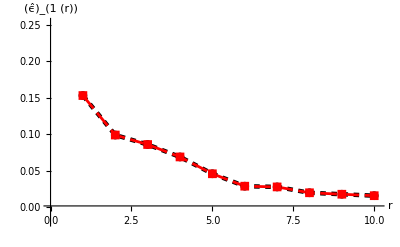

```mathematica
F1=ListPlot[{V[1],V[2]},Joined->True,PlotRange->{{0,10.1},{-0.02,0.253}},AxesStyle->Directive[Black,13],AxesOrigin->{0,0.002},PlotStyle->{{Thickness[0.008],Dashing[{0.01,0.01}],Black},{Thickness[0.005],Dashing[{0.03,0.01}],Red},
{Thickness[0.005],Dashing[{0.02,0.02}],Blue},{Thickness[0.009],Dashing[{0.012,0.02}],Darker[Green]},{Thickness[0.007],Orange},
{Thickness[0.005],Red}},PlotLegend->{Style[ "(D-i)",FontSize->10],Style[ "(D-ii)",FontSize->10],Style[ "BC-GSVM with (γ̂)_0",FontSize->10],Style[ "GSVM with (γ̂)_0",FontSize->10],Style[ "(9) for (c)",FontSize->14]},LegendPosition->{0,0.1},LegendTextSpace->4,LegendSize->{0.65,0.37},LegendShadow->{0.02,0.02},AxesLabel->{"r","(ϵ̂)_(1 (r))"},PlotMarkers->Automatic]
```

```mathematica
V[1]=Table[{i,Part[Part[T2,1],i]},{i,1,10}]
```

{{1,0.157},{2,0.105},{3,0.066},{4,0.053},{5,0.047},{6,0.039},{7,0.026},{8,0.023},{9,0.021},{10,0.014}}

```mathematica
V[2]=Table[{i,Part[Part[T2,2],i]},{i,1,10}]
```

{{1,0.157},{2,0.105},{3,0.066},{4,0.053},{5,0.047},{6,0.039},{7,0.026},{8,0.023},{9,0.021},{10,0.014}}

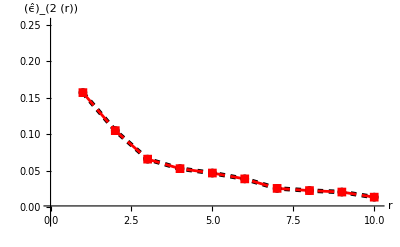

```mathematica
F2=ListPlot[{V[1],V[2]},Joined->True,PlotRange->{{0,10.1},{-0.02,0.253}},AxesStyle->Directive[Black,13],AxesOrigin->{0,0.002},PlotStyle->{{Thickness[0.008],Dashing[{0.01,0.01}],Black},{Thickness[0.005],Dashing[{0.03,0.01}],Red},
{Thickness[0.005],Dashing[{0.02,0.02}],Blue},{Thickness[0.009],Dashing[{0.012,0.02}],Darker[Green]},{Thickness[0.007],Orange},
{Thickness[0.005],Red}},PlotLegend->{Style[ "(D-i)",FontSize->10],Style[ "(D-ii)",FontSize->10],Style[ "BC-GSVM with (γ̂)_0",FontSize->10],Style[ "GSVM with (γ̂)_0",FontSize->10],Style[ "(9) for (c)",FontSize->14]},LegendPosition->{0,0.1},LegendTextSpace->4,LegendSize->{0.65,0.37},LegendShadow->{0.02,0.02},AxesLabel->{"r","(ϵ̂)_(2 (r))"},PlotMarkers->Automatic]
```